```mathematica
(*лаб 10 - метод Ньютона (метод касательных)*)
```

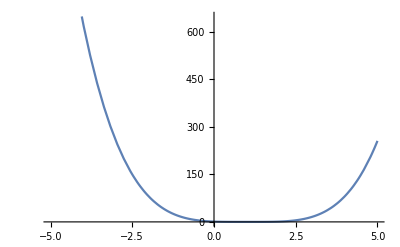

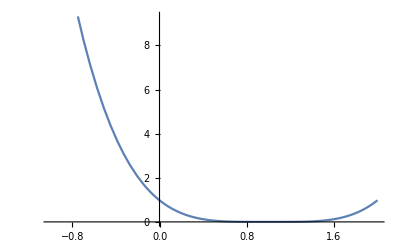

{{xx→0.9},{xx→0.9},{xx→1.1},{xx→1.1}}

```mathematica
eps=0.5*10^-5;
δ=0.0000005;
f[x_]:=x^4-4 x^3+5.98 x^2-3.96x+0.9801;
fx[x_]:=4 x^3-12 x^2+11.96x-3.96;
fxx[x_]:=12 x^2-24x+11.96;

Plot[f[x],{x,-5,5}]
Plot[f[x],{x,-1,2}]
Solve[f[xx]==0,xx]//N
x0list={0.5,1.5};
multiplicities={1,1};
n=2;

nextx[currentx_]:=currentx-2*(f[currentx]/fx[currentx]);
```

```mathematica
For[i=0,i<n,i++,
	x0=x0list[[i+1]]; 

(*nextx[currentx_]:=(x0*f[currentx]-currentx*f[x0])/(f[currentx]-f[x0]);*)
	
	B=Abs[1/fx[x0]];
	η=Abs[f[x0]/fx[x0]];
	K=First[FindMaximum[{Abs[fxx[x]],Abs[x-x0]≤δ},{x,x0}]];
	Print["h = ",B*η*K];
	
	Subscript[x, n]=x0;
	Subscript[x, n+1]=nextx[Subscript[x, n]];
	iterations=0;
	
	While[Abs[Subscript[x, n+1]-Subscript[x, n]]>eps,
		{Subscript[x, n],Subscript[x, n+1]}={Subscript[x, n+1],nextx[Subscript[x, n+1]]};
		iterations++;
	];
	Print[i+1,"й корень = ",Subscript[x, n+1]//N,", ", iterations, " итераций, f(x) = ", f[Subscript[x, n+1]]//N]
];
```

h = 0.739897

1й корень = 0.9, 5 итераций, f(x) = 4.44089×10^-16

h = 0.74

2й корень = 1.1, 5 итераций, f(x) = 1.33227×10^-15